# Primer examen de Métodos numéricos Nombre: Solución

## Programas usados en el examen

```mathematica
bisec[f_,a1_,b1_,n_,pre_]:=Module[{a=SetPrecision[a1,pre],b=SetPrecision[b1,pre]},
list=Table[c=(a+b)/2;If[(f/.x->c)(f/.x->b)<0,a=c,b=c],{n}];
error=Abs[list[[n]]-list[[n-1]]]/list[[n]];{c,error}
]
```

## 1- (6.15)

```mathematica
R=0.518;pc=4600;Tc=191;a=0.427(R^2 Tc^2.5)/pc;b=0.0866R Tc/pc;
T=-40+273.15;
P=65;
f=(R T)/(x-b)-a/(x(x+b)√T)-P
```

-65+120.772/(-0.00186262+x)-0.822423/(x (0.00186262+x))

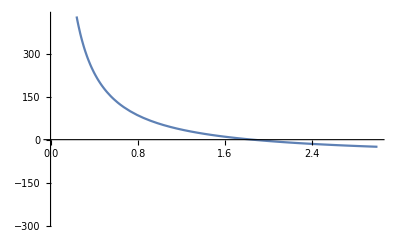

```mathematica
Plot[f,{x,0,3}]
```

```mathematica
bisec[f,0,3,20,10][[1]]
masa=3/bisec[f,0,3,20,10][[1]]
```

1.853075981

1.618929839

## 2 - (6.17)

```mathematica
w=10;y0=5;y=15;xx=50;
f=x/w Cosh[w/x xx]+y0-x/w-y
```

-10-x/10+1/10 x Cosh[500/x]

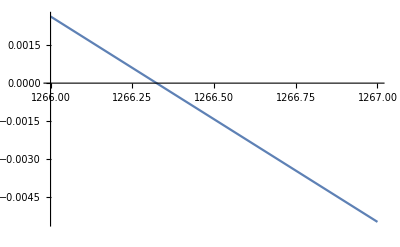

```mathematica
Plot[f,{x,1266,1267}]
```

```mathematica
Ta=bisec[f,1266,1267,20,10][[1]]
```

1266.324342

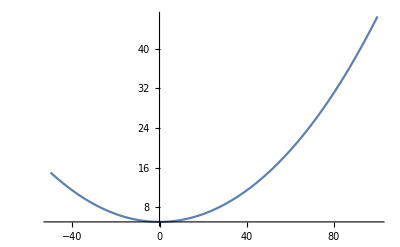

```mathematica
g=Ta/w Cosh[w/Ta equis]+y0-Ta/w;
Plot[g,{equis,-50,100}]
```

## 3 - (6.21)

90 tan(x)-44.145 sec^2(x)+0.8

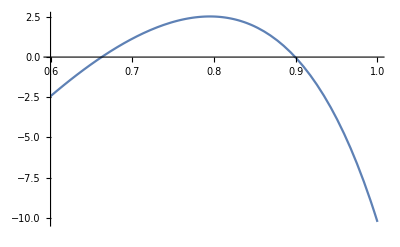

```mathematica
v0=30;xx=90;y0=1.8;y=1;
f=Tan[x]xx-9.81/(2 v0^2 Cos[x]^2)xx^2+y0-y
Plot[f,{x,0.6,1}]
```

```mathematica
bisec[f,0.6,0.7,20,10][[1]] 180/π
bisec[f,0.8,0.92,20,10][[1]] 180/π
```

37.95898395

51.53173588

## 4 - (Newton-Raphson) Este programa calcula las raíces de una función haciendo uso de la aproximación de la derivada de la función. Sólo requiere una función, una aproximación de la raíz y el número de iteraciones. Use el programa para graficar el valor de la raíz vs. el error porcentual de la raíz. Usa la función-ejemplo que se da.

```mathematica
new[f_,a1_,n_]:=Module[{a=a1},
p=Table[b=a;a=a-(f/.x->a)/(D[f,x]/.x->a);error=Abs[(b-a)/a]100;{a,error},{n}];
Print[ListPlot[p]];
p
]
```

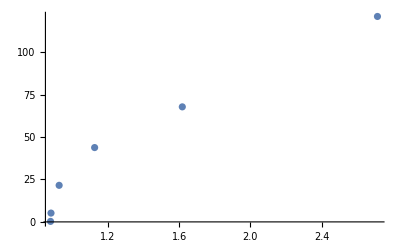

(2.71377 | 121.095
1.61716 | 67.8107
1.12449 | 43.8126
0.925062 | 21.5586
0.879336 | 5.20009
0.876735 | 0.296706)

```mathematica
new[Sin[x]-x^2,6.,6]
```

## 5 - (Programa) Hacer un programa que halle los máximos y mínimos y, los puntos silla de una función de dos variables. Corran la función-ejemplo. -Graphics-

```mathematica
Clear[x,y]
f=x^3+y^3-3 x^2-3 y^2-9x;
```

```mathematica
maxmin[f_]:=Module[{},
pri=D[f,{{x,y}}];
sol=Solve[{pri[[1]]==0,pri[[2]]==0},{x,y},Reals];
dis=(D[pri[[1]],x])(D[pri[[2]],y])-(D[pri[[1]],y])^2;
Table[If[(dis/.sol[[i]])<0,Print["Punto silla en :", {x,y}/.sol[[i]]],If[(D[pri[[1]],x]/.sol[[i]])>0,Print["Mínimo en :" ,{x,y}/.sol[[i]]],Print["Máximo en :" ,{x,y}/.sol[[i]]]]],{i,Length[sol]}];
]
```

```mathematica
maxmin[f]
```

Máximo en :{-1,0}

Punto silla en :{-1,2}

Punto silla en :{3,0}

Mínimo en :{3,2}